```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
T1[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
(*Import leads *)
```

```mathematica
Lead=Table[ToExpression[Import["~/PhD_new/PhD/fwi/AGNR/7AGNR/Leads/lead_"<>ToString[X]<>".dat"]],{X,Range[0,3,0.01]}]
```

{{{0.-0.0000823223 ⅈ,-0.573223+0. ⅈ,0.+0.000025 ⅈ,0.25+0. ⅈ,0.-2.8033×10^-13 ⅈ,-0.0732233+0. ⅈ,0.-7.32233×10^-6 ⅈ,0.0732233+0. ⅈ,0.+0.0000146447 ⅈ,-0.176777+0. ⅈ,0.-0.0000323223 ⅈ,0.323223+0. ⅈ,0.+0.0000396447 ⅈ,-0.426777+0. ⅈ},{1},10,{1},{-0.426777+0. ⅈ,0.+1035.53 ⅈ,0.323223+0. ⅈ,9,-0.46967+0. ⅈ,0.-1035.53 ⅈ}},300}
 |  |  |  |

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Lead[[ω*100+1]]
```

```mathematica
(*Or Generate leads using recursive algorithm*)
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:=Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
```

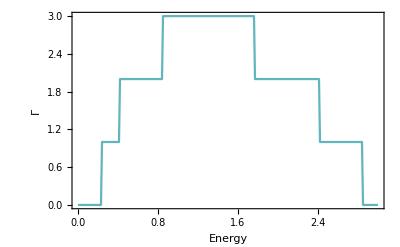

```mathematica
ListLinePlot[ParallelTable[{ω,tr[ω,0.0001,1,0]},{ω,Range[0,3,0.01]}],Frame->True,PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]],FrameLabel->{{HoldForm[Γ],None},{HoldForm[Energy],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",10.5,GrayLevel[0]}]
```

```mathematica
Export["test_5.dat",ParallelTable[{ω,inputspectra[ω,0.5,50]},{ω,Range[0,3,0.01]}]]
```

test_5.dat

```mathematica
(* Conductance using Kubo Formula *)
```

```mathematica
inputspectra[ω_,ϵ1_,size_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}]},
tra:=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ1]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ1]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ1]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ1]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ1]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ1]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ1]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001-0]]]},
(* Distribution of impurities inside the device region *)
lista={{imp,imp,imp,imp,imp,imp,imp,imp,imp,imp12,imp,imp5,imp13,imp,imp,imp2,imp,imp,imp,imp,imp,imp,imp10,imp2,imp14,imp,imp1,imp,imp,imp6,imp5,imp,imp7,imp1,imp10,imp12,imp8,imp,imp,imp4,imp1,imp6,imp,imp11,imp7,imp4,imp,imp,imp11,imp,imp14,imp,imp,imp10,imp12,imp,imp,imp,imp,imp9,imp,imp,imp7,imp14,imp9,imp13,imp,imp,imp6,imp,imp,imp,imp,imp1,imp,imp3,imp8,imp,imp,imp,imp5,imp3,imp,imp,imp3,imp,imp,imp2,imp,imp9,imp,imp8,imp4,imp,imp,imp,imp,imp13,imp,imp11}};
b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,size}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>tr[ω,0.0001,1,0],tr[ω,0.0001,1,0],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra]
```

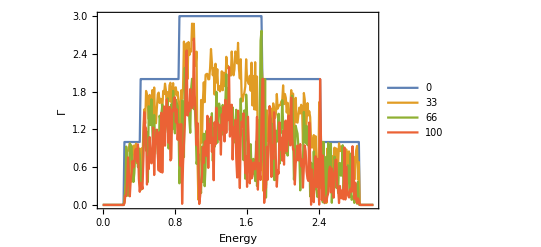

```mathematica
ListLinePlot[Table[ParallelTable[{ω,inputspectra[ω,0.5,size]},{ω,Range[0,3,0.01]}],{size,0,100,33}],Frame->True,(*PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]],*)FrameLabel->{{HoldForm[Γ],None},{HoldForm[Energy],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",10.5,GrayLevel[0]},PlotLegends->{0,33,66,100}]
```

```mathematica
Configuraional Averaging
```

```mathematica
F[n_]:= {n,n}
```

```mathematica
impurity[ω_,δ_,t_,ϵ_,ϵ1_,n_]:=Module[{b=β[ω,δ,t,ϵ]},ReplacePart[b,Table[F[RandomSample[{RandomInteger[{1,14}]},1]]//Flatten,n]->ω+ⅈ*δ-ϵ1]]
```

```mathematica
CAvg[ω_,δ_,t_,ϵ_,ϵ1_,n_,num_,size_]:= Module[{Tin=T1[1],T=TT[1]},
tra:=Module[{},
(* Distribution of impurities inside the device region *)
lista={RandomSample[Join[Table[impurity[ω,0.0001,1,0,ϵ1,1],num],Table[impurity[ω,0.0001,1,0,0,1],size-num]]]};
b=Module[{},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-Inverse[lista[[1,ζ]]].ConjugateTranspose[Tin].J.Tin].Inverse[lista[[1,ζ]]],{ζ,1,size}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>tr[ω,0.0001,1,0],tr[ω,0.0001,1,0],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]];
b];
tra]
```

```mathematica
CAvg[1,0.0001,1,0,0.5,1,50,100]
```

1.51836

```mathematica
Table[{ω,CAvg[ω,0.0001,1,0,0.5,42,1,50,100]},{ω,Range[0,3,0.01]}]
```

```mathematica
ListLinePlot[Table[{ω,CAvg[ω,0.0001,1,0,0.5,42,1,50,100]},{ω,Range[0,3,0.01]}]]
```

-Graphics-

```mathematica
(* Size= 100 , M = Number of configurations considered for averaging = 2500 *)
```

```mathematica
avg= Compile[{ω,num},ParallelTable[CAvg[ω,0.0001,1,0,0.5,1,num,100],2500],CompilationOptions->{"ExpressionOptimization" -> True},Parallelization->True,CompilationTarget->"C"]
```

CompiledFunction[…]

```mathematica
(*Generate Configurational average spectras and export! 
num = number of impurities inside the device *)
```

```mathematica
Table[Export["",Table[{ω,avg[ω,num]},{ω,Range[0,3,0.01]}]],{num,Range[5,85,10]}]
```

```mathematica
(*Interpolation (machine learning??)*)
```

```mathematica
(*Import generated averages from above section*)
```

```mathematica
transmission = Table[Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/100unitcells/resolve/test"<>ToString[X]<>".dat"],{X,Range[5,85,10]}]
```

{{{0.,2.79841×10^-7},{0.01,2.72438×10^-7},{0.02,2.76055×10^-7},{0.03,2.8154×10^-7},{0.04,2.86312×10^-7},{0.05,2.93608×10^-7},{0.06,3.05841×10^-7},{0.07,3.15627×10^-7},{0.08,3.3353×10^-7},283,{2.92,4.55387×10^-7},{2.93,3.50822×10^-7},{2.94,2.79217×10^-7},{2.95,2.26938×10^-7},{2.96,1.88087×10^-7},{2.97,1.58019×10^-7},{2.98,1.34547×10^-7},{2.99,1.15807×10^-7},{3.,1.01074×10^-7}},7,{1}}
 |  |  |  |

```mathematica
trainingset[ω_]:=Table[5+10*(n-1)->transmission[[n]][[ω*100+1,2]],{n,Range[1,9,1]}]
```

```mathematica
data[num_,ω_]:=Module[{P},P=Predict[trainingset[ω],Method->"NeuralNetwork"]; P[num]]
```

```mathematica
(*This allows us to generate average specta for continuous number of impurities *)
```

```mathematica
Mean[ParallelTable[CAvg[1,0.0001,1,0,0.5,1,50,100],5000]]//AbsoluteTiming
```

{44.6249,1.5082}

```mathematica
data[50,1]//AbsoluteTiming
```

{5.94424,1.46416}

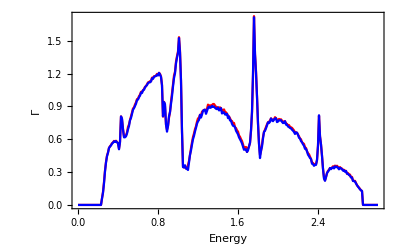

```mathematica
Show[ListLinePlot[Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/100unitcells/resolve/test55.dat"],PlotStyle->Red,Frame->True,PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]],FrameLabel->{{HoldForm[Γ],None},{HoldForm[Energy],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",10.5,GrayLevel[0]}],ListLinePlot[Table[{ω,data[55,ω]},{ω,Range[0,3,0.01]}],PlotStyle->Blue]]
```

```mathematica
Misfit Function
```

```mathematica
(* Import interpolated averages *)
```

```mathematica
transmission100= Table[Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/100unitcells/resolve/test"<>ToString[X]<>".dat"],{X,Range[5,85,2]}]
```

Import::nffil: File /home/shardulmukim/PhD/fwi/AGNR/7AGNR/100unitcells/resolve/test5.dat not found during Import.

Import::nffil: File /home/shardulmukim/PhD/fwi/AGNR/7AGNR/100unitcells/resolve/test7.dat not found during Import.

Import::nffil: File /home/shardulmukim/PhD/fwi/AGNR/7AGNR/100unitcells/resolve/test9.dat not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}

```mathematica
(* Generate input spectra using kubo formula *)
```

```mathematica
input= Table[ParallelTable[{ω,inputspectra[ω,0.5,100]},{ω,Range[0,3,0.01]}],100]
```

{{{0.,2.8×10^-7},{0.01,5.16712×10^-8},{0.02,2.83264×10^-7},{0.03,2.87439×10^-7},{0.04,2.93463×10^-7},{0.05,3.01536×10^-7},{0.06,3.11935×10^-7},{0.07,3.25045×10^-7},{0.08,3.41391×10^-7},283,{2.92,4.6079×10^-7},{2.93,3.54437×10^-7},{2.94,2.8098×10^-7},{2.95,2.28152×10^-7},{2.96,1.88907×10^-7},{2.97,1.58966×10^-7},{2.98,1.35611×10^-7},{2.99,1.17044×10^-7},{3.,1.02043×10^-7}},98,{1}}
 |  |  |  |

```mathematica
Misfit[x_,y_,n_]:=Module[{m5 = input[[n]]},ρ1:= Table[Module[{B1=Transpose[{m5[[1;;300]][[;;,1]],100(m5[[1;;300,2]]-transmission100[[ξ]][[1;;300,;;]][[;;,2]])^2}]},Integrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)],{ξ,41}]; 
Transpose[Join[{Range[5,85,2]},{ρ1}]]]
```

```mathematica
Misfit[2.75,0.,11]
```

{{5,1.11817},{7,0.91521},{9,0.757861},{11,0.63398},{13,0.535305},{15,0.45536},{17,0.390342},{19,0.337636},{21,0.293519},{23,0.257535},{25,0.228839},{27,0.205541},{29,0.187088},{31,0.171541},{33,0.161349},{35,0.153364},{37,0.146054},{39,0.142945},{41,0.139989},{43,0.140467},{45,0.14104},{47,0.142151},{49,0.145398},{51,0.148378},{53,0.153118},{55,0.158354},{57,0.164478},{59,0.169579},{61,0.175676},{63,0.181392},{65,0.187352},{67,0.19376},{69,0.199789},{71,0.207357},{73,0.214103},{75,0.219639},{77,0.226812},{79,0.232498},{81,0.239189},{83,0.246054},{85,0.251049}}

```mathematica
(*Number of impurities obtained from the inversion for given input spectra*)
```

```mathematica
Table[Misfit[2.75,0,n][[Position[Misfit[2.75,0,n],Min[Misfit[2.75,0,n]]][[1,1]]]],{n,100}]
```

{{47,0.137902},{45,0.14688},{45,0.134238},{43,0.133453},{43,0.136068},{43,0.123634},{41,0.144587},{43,0.143977},{43,0.142133},{39,0.125987},{41,0.139989},{43,0.116007},{41,0.154824},{43,0.124223},{41,0.124322},{39,0.128029},{47,0.125809},{43,0.133357},{43,0.110319},{43,0.129125},{43,0.116526},{43,0.14218},{47,0.163235},{45,0.131681},{45,0.13698},{41,0.15125},{45,0.145527},{47,0.132367},{43,0.126166},{39,0.127407},{45,0.131273},{45,0.125321},{47,0.152259},{47,0.147723},{45,0.132715},{45,0.132664},{43,0.129684},{39,0.119487},{43,0.153135},{45,0.127782},{37,0.15048},{41,0.137563},{41,0.119651},{43,0.143111},{45,0.153866},{41,0.135766},{41,0.146521},{41,0.131101},{41,0.103069},{41,0.118465},{45,0.135073},{45,0.133369},{45,0.117376},{43,0.124894},{45,0.143631},{45,0.151417},{47,0.129575},{45,0.131588},{47,0.155161},{43,0.132751},{45,0.124034},{41,0.146746},{47,0.124189},{49,0.131882},{45,0.162905},{47,0.175007},{43,0.13813},{41,0.109266},{47,0.113629},{41,0.13005},{43,0.127215},{47,0.15577},{45,0.117928},{39,0.113305},{43,0.133559},{43,0.132052},{43,0.137933},{43,0.13655},{43,0.115283},{43,0.140312},{41,0.146326},{41,0.134415},{45,0.133353},{43,0.132024},{41,0.151885},{43,0.115376},{41,0.13483},{47,0.118475},{43,0.13614},{45,0.104488},{43,0.128015},{41,0.107363},{43,0.138926},{43,0.14259},{45,0.136347},{43,0.140149},{43,0.131321},{41,0.133123},{43,0.11857},{43,0.121488}}

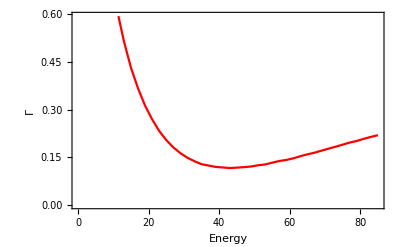

```mathematica
ListPlot[Misfit[2.75,0,12],Joined->True,PlotStyle->Red,Frame->True,PlotStyle->RGBColor[RandomReal[{0,1}],RandomReal[{0,1}],RandomReal[{0,1}]],FrameLabel->{{HoldForm[Γ],None},{HoldForm[Energy],None}},PlotLabel->None,LabelStyle->{FontFamily->"Times New Roman",10.5,GrayLevel[0]}]
```

```mathematica
list[num_,m_]:=Transpose[Join[{Range[1,100]},{RandomSample[Join[Table[0,100-num],Table[RandomInteger[{1,2*m}],num]]]}]]
```

```mathematica
Table[RandomInteger[{1,2*7}],51]
```

{9,14,7,3,7,10,2,12,7,4,3,14,9,11,6,14,7,1,4,7,11,11,7,7,2,7,7,2,4,5,7,4,4,7,3,2,14,2,13,12,5,13,6,13,9,9,2,12,9,10,3}

```mathematica
Length[Table[RandomInteger[{1,2*7}],51]]
```

51

```mathematica
list[51,7]
```

{{1,0},{2,8},{3,1},{4,3},{5,12},{6,5},{7,0},{8,0},{9,0},{10,2},{11,0},{12,7},{13,11},{14,7},{15,0},{16,6},{17,0},{18,0},{19,13},{20,0},{21,3},{22,0},{23,13},{24,0},{25,0},{26,0},{27,5},{28,14},{29,0},{30,0},{31,5},{32,1},{33,0},{34,0},{35,10},{36,3},{37,8},{38,0},{39,0},{40,0},{41,13},{42,14},{43,0},{44,0},{45,13},{46,5},{47,6},{48,0},{49,0},{50,0},{51,0},{52,11},{53,0},{54,0},{55,0},{56,14},{57,4},{58,6},{59,7},{60,10},{61,5},{62,2},{63,0},{64,0},{65,10},{66,10},{67,0},{68,0},{69,7},{70,11},{71,5},{72,0},{73,0},{74,7},{75,3},{76,0},{77,0},{78,13},{79,9},{80,0},{81,0},{82,8},{83,10},{84,0},{85,3},{86,0},{87,4},{88,9},{89,0},{90,12},{91,14},{92,0},{93,0},{94,5},{95,0},{96,7},{97,0},{98,0},{99,0},{100,0}}

```mathematica
ListPlot[%52,Joined->True]
```

```mathematica
dist=Table[list[4,7],5000]
```

{{{1,0},{2,10},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0},{13,0},{14,0},{15,0},71,{87,0},{88,0},{89,0},{90,0},{91,0},{92,0},{93,0},{94,0},{95,0},{96,9},{97,0},{98,0},{99,0},{100,0}},4999}
 |  |  |  |

```mathematica
CAvg[ω_,δ_,t_,ϵ_,ϵ1_,number_]:= Module[{Tin=T1[1],T=TT[1]},
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-Inverse[Module[{κ=β[ω,δ,t,ϵ],n= dist[[number]][[loc1,2]]},ReplacePart[κ,{{n,n}}->ω+ⅈ*0.0001-ϵ1]]].ConjugateTranspose[Tin].J.Tin].Inverse[Module[{κ=β[ω,δ,t,ϵ],n= dist[[number]][[loc1,2]]},ReplacePart[κ,{{n,n}}->ω+ⅈ*0.0001-ϵ1]]],{loc1,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];If[Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]>tr[ω,0.0001,1,0],tr[ω,0.0001,1,0],Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]]]
```

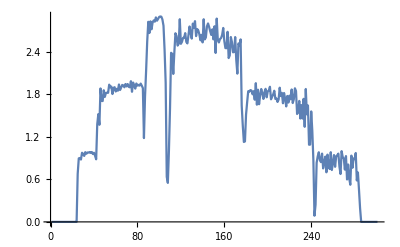

```mathematica
ListLinePlot[Table[CAvg[ω,0.0001,1,0,0.5,1],{ω,Range[0,3,0.01]}]]
```

```mathematica
Clear[CAvg]
```

```mathematica
f[xyz_]:=ParallelTable[CAvg[1.4,0.0001,1,0,0.5,x],{x,xyz}]
```

```mathematica
Mean[f[30]]
```

1.79003

```mathematica
Monitor[Table[{x,Mean[f[x]]},{x,10,1000,10}],x]
```

{{10,1.38275},{20,1.52479},{30,1.5952},{40,1.61763},{50,1.55089},{60,1.56417},{70,1.58775},{80,1.58362},{90,1.55853},{100,1.55798},{110,1.55042},{120,1.55966},{130,1.55084},{140,1.5492},{150,1.55779},{160,1.56081},{170,1.55686},{180,1.56478},{190,1.56747},{200,1.57973},{210,1.57036},{220,1.57274},{230,1.57542},{240,1.57985},{250,1.58406},{260,1.58132},{270,1.5869},{280,1.5907},{290,1.59072},{300,1.59243},{310,1.59713},{320,1.60081},{330,1.59801},{340,1.59885},{350,1.60157},{360,1.60037},{370,1.60011},{380,1.60118},{390,1.59916},{400,1.59866},{410,1.59335},{420,1.58877},{430,1.58677},{440,1.58508},{450,1.59069},{460,1.59098},{470,1.59235},{480,1.59298},{490,1.59376},{500,1.59506},{510,1.58932},{520,1.59338},{530,1.59784},{540,1.59367},{550,1.59289},{560,1.59055},{570,1.59555},{580,1.59042},{590,1.58794},{600,1.58714},{610,1.58876},{620,1.58969},{630,1.58943},{640,1.58877},{650,1.58879},{660,1.58831},{670,1.59011},{680,1.58823},{690,1.588},{700,1.58747},{710,1.58623},{720,1.58724},{730,1.58854},{740,1.59073},{750,1.59014},{760,1.58802},{770,1.58825},{780,1.58917},{790,1.59179},{800,1.59306},{810,1.59238},{820,1.59344},{830,1.59393},{840,1.59258},{850,1.59404},{860,1.59499},{870,1.59397},{880,1.59407},{890,1.59423},{900,1.59267},{910,1.59304},{920,1.59158},{930,1.59109},{940,1.59066},{950,1.58965},{960,1.59085},{970,1.59205},{980,1.59041},{990,1.59234},{1000,1.59095}}

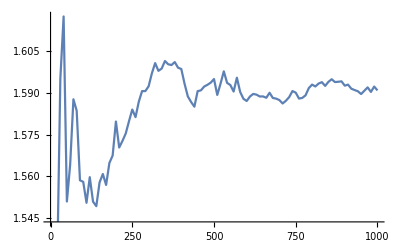

```mathematica
ListPlot[%48,Joined->True]
```

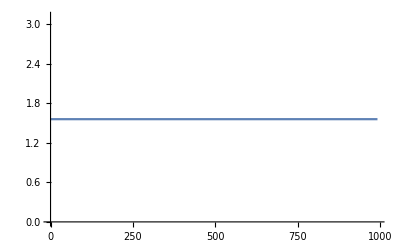

```mathematica
ListPlot[%25,Joined->True]
```

```mathematica
Table[f[xyz],{xyz,1000}]
```

```mathematica
Table[{ω,Mean[ParallelTable[CAvg[ω,0.0001,1,0,0.5,number,100],{number,5000}]]},{ω,Range[0,1.5,0.01]}]
```

{{0.,2.59189×10^-7},{0.01,2.43112×10^-7},{0.02,2.52774×10^-7},{0.03,2.63663×10^-7},{0.04,2.71701×10^-7},{0.05,2.82979×10^-7},{0.06,2.9409×10^-7},{0.07,3.06786×10^-7},{0.08,3.22858×10^-7},{0.09,3.43262×10^-7},{0.1,3.67156×10^-7},{0.11,3.98205×10^-7},{0.12,4.37321×10^-7},{0.13,4.88196×10^-7},{0.14,5.55459×10^-7},{0.15,6.45731×10^-7},{0.16,7.70368×10^-7},{0.17,9.5055×10^-7},{0.18,1.23054×10^-6},{0.19,1.70448×10^-6},{0.2,2.61401×10^-6},{0.21,4.76766×10^-6},{0.22,0.000012425},{0.23,0.000111064},{0.24,0.0589862},{0.25,0.129286},{0.26,0.235157},{0.27,0.343936},{0.28,0.423662},{0.29,0.473817},{0.3,0.514108},{0.31,0.534487},{0.32,0.556006},{0.33,0.581762},{0.34,0.590257},{0.35,0.595804},{0.36,0.605952},{0.37,0.608486},{0.38,0.618323},{0.39,0.604533},{0.4,0.580712},{0.41,0.520006},{0.42,0.59344},{0.43,0.821139},{0.44,0.746669},{0.45,0.675238},{0.46,0.633327},{0.47,0.638185},{0.48,0.66769},{0.49,0.710313},{0.5,0.746254},{0.51,0.777527},{0.52,0.820043},{0.53,0.861997},{0.54,0.885735},{0.55,0.925172},{0.56,0.936059},{0.57,0.970686},{0.58,0.985391},{0.59,1.00964},{0.6,1.02267},{0.61,1.04535},{0.62,1.06139},{0.63,1.09109},{0.64,1.09775},{0.65,1.11573},{0.66,1.12228},{0.67,1.13312},{0.68,1.15358},{0.69,1.15592},{0.7,1.17104},{0.71,1.18037},{0.72,1.17944},{0.73,1.18214},{0.74,1.20496},{0.75,1.21303},{0.76,1.22125},{0.77,1.22916},{0.78,1.23478},{0.79,1.24417},{0.8,1.25179},{0.81,1.25335},{0.82,1.24913},{0.83,1.23309},{0.84,1.15919},{0.85,0.834597},{0.86,0.972707},{0.87,0.882087},{0.88,0.745918},{0.89,0.715775},{0.9,0.774501},{0.91,0.836964},{0.92,0.914285},{0.93,1.0157},{0.94,1.09138},{0.95,1.16951},{0.96,1.24196},{0.97,1.31809},{0.98,1.37818},{0.99,1.44523},{1.,1.49648},{1.01,1.58368},{1.02,1.47138},{1.03,1.20067},{1.04,0.713831},{1.05,0.367772},{1.06,0.34011},{1.07,0.3434},{1.08,0.335221},{1.09,0.34026},{1.1,0.383627},{1.11,0.432716},{1.12,0.505612},{1.13,0.568012},{1.14,0.625655},{1.15,0.685814},{1.16,0.718684},{1.17,0.767703},{1.18,0.810443},{1.19,0.82846},{1.2,0.860446},{1.21,0.88601},{1.22,0.902669},{1.23,0.911175},{1.24,0.930332},{1.25,0.948033},{1.26,0.951526},{1.27,0.948496},{1.28,0.946496},{1.29,0.966544},{1.3,0.973638},{1.31,0.978687},{1.32,0.983089},{1.33,0.984687},{1.34,0.98714},{1.35,0.980658},{1.36,0.993647},{1.37,0.988225},{1.38,0.981281},{1.39,0.980655},{1.4,0.975652},{1.41,0.980049},{1.42,0.96537},{1.43,0.962983},{1.44,0.940768},{1.45,0.943898},{1.46,0.93537},{1.47,0.938243},{1.48,0.915222},{1.49,0.906137},{1.5,0.890187}}

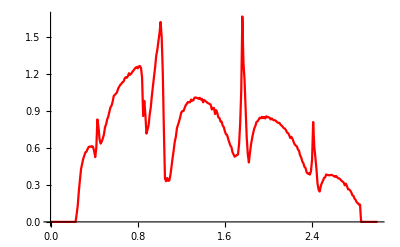

```mathematica
ListLinePlot[Import["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/100unitcells/resolve/test49.dat"],PlotStyle->Red]
```

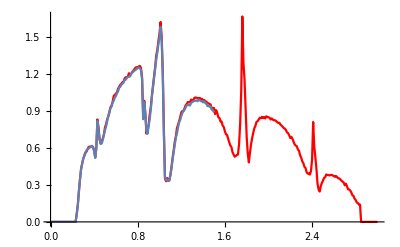

```mathematica
Show[%38,%37]
```

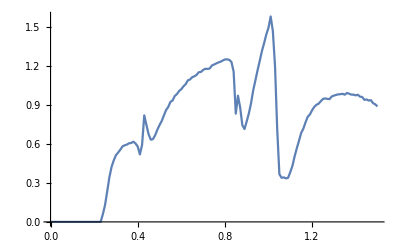

```mathematica
ListPlot[%36,Joined->True]
```

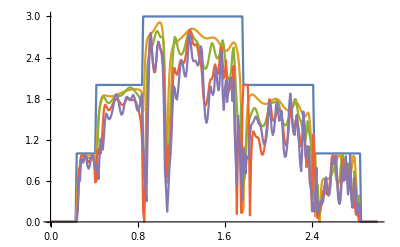

```mathematica
ListLinePlot[Table[Table[{ω,CAvg[ω,0.0001,1,0,0.5,1,size]},{ω,Range[0,3,0.01]}],{size,Range[4,30,6]}]]
```

```mathematica
(*device[ω_,δ_,t_,ϵ_,m_,number_]:=Module[{},
sl1= Module[{J=SL[ω,δ,t,-0.75,1,m]},Do[J=Inverse[IdentityMatrix[2m]-Inverse[Module[{κ=β[ω,δ,t,-0.75,1,m],n= dist[[number]][[loc1,2]]},ReplacePart[κ,{{n,n}}->ω+ⅈ*0.0001-ϵ]]].ConjugateTranspose[T1[1,m]].J.T1[1,m]].Inverse[Module[{κ=β[ω,δ,t,-0.75,1,m],n= dist[[number]][[loc1,2]]},ReplacePart[κ,{{n,n}}->ω+ⅈ*0.0001-ϵ]]],{loc1,100}];
 J=J];
il1:=Inverse[IdentityMatrix[2m]-sl1.ρ[1,m].SR[ω,δ,t,1,-0.75,m].ConjugateTranspose[ρ[1,m]]].sl1;
ir1:=Inverse[IdentityMatrix[2m]-SR[ω,δ,t,1,-0.75,m].ρ[1,m].sl1.ρ[1,m]].SR[ω,δ,t,1,-0.75,m];gdd1:=il1-ConjugateTranspose[il1];grr1:= ir1-ConjugateTranspose[ir1];Gnonlocal1:= SR[ω,δ,t,1,-0.75,m].ρ[1,m].il1;GNON1:=Gnonlocal1-ConjugateTranspose[Gnonlocal1];tr1=Abs[Tr[gdd1.ρ[1,m].grr1.ρ[1,m]-ρ[1,m].GNON1.ρ[1,m].GNON1]];If[tr1>pris[ω,0.0001,1,-0.75,1,9],pris[ω,0.0001,1,-0.75,1,9],tr1]]*)
```